{{a[n]→1/2 (2+n+n^2)}}

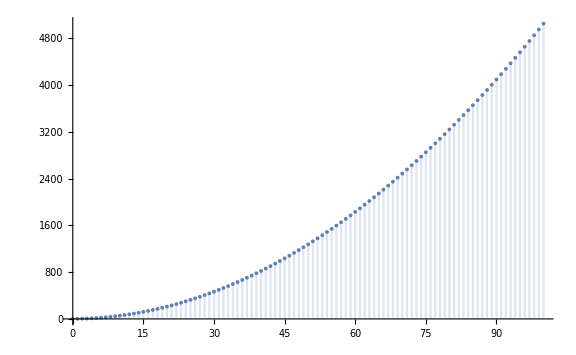

Result {lines, regions}: 
{{0,1},{1,2},{2,4},{3,7},{4,11},{5,16},{6,22},{7,29},{8,37},{9,46},{10,56},{11,67},{12,79},{13,92},{14,106},{15,121},{16,137},{17,154},{18,172},{19,191},{20,211},{21,232},{22,254},{23,277},{24,301},{25,326},{26,352},{27,379},{28,407},{29,436},{30,466},{31,497},{32,529},{33,562},{34,596},{35,631},{36,667},{37,704},{38,742},{39,781},{40,821},{41,862},{42,904},{43,947},{44,991},{45,1036},{46,1082},{47,1129},{48,1177},{49,1226},{50,1276},{51,1327},{52,1379},{53,1432},{54,1486},{55,1541},{56,1597},{57,1654},{58,1712},{59,1771},{60,1831},{61,1892},{62,1954},{63,2017},{64,2081},{65,2146},{66,2212},{67,2279},{68,2347},{69,2416},{70,2486},{71,2557},{72,2629},{73,2702},{74,2776},{75,2851},{76,2927},{77,3004},{78,3082},{79,3161},{80,3241},{81,3322},{82,3404},{83,3487},{84,3571},{85,3656},{86,3742},{87,3829},{88,3917},{89,4006},{90,4096},{91,4187},{92,4279},{93,4372},{94,4466},{95,4561},{96,4657},{97,4754},{98,4852},{99,4951},{100,5051}}

```mathematica
(*Clear everything*)
Clear["`*"];
(*Initial condition: 0 line, 1 plane; 1 line, 2 half-planes (regions) *)
iv1=a[0]==1;
iv2=a[1]==2;
(*Since there is no parallel nor *** line, one new line will cross n lines, cross n regions plus the final empty halfplane, divides it into 2 halfplanes *)
rr=a[n+1]==a[n]+n+1;
(*Solve it by Mathematica *)
sol=RSolve[{rr,iv1,iv2},a[n],n] // Simplify
a[n_]=a[n]/.sol[[1]];
DiscretePlot[Evaluate[a[n]]/.sol[[1]],{n,0,100}]
(*Exporting and ploting*)

data = Table[{n,a[n]},{n,0,100,1}];
Print["Result {lines, regions}: \n",data];
```